# Position projections

## Definitions

## DTQW Environment

```mathematica
$DTQWEnvIcon=Graphics[{
Thick,
Circle[],
PointSize[Large],
Point[{0,0}]
},
ImageSize->Dynamic[{
Automatic,
3.5 CurrentValue["FontCapHeight"]/AbsoluteCurrentValue[Magnification]
}]
];
```

```mathematica
DTQWEnvAscQ[asc_?AssociationQ]:=And[
AllTrue[{"Type","Decoherent"},KeyExistsQ[asc,#]&],
Or[KeyExistsQ[asc,"Unitary"],AllTrue[{"Shift","Coin"},KeyExistsQ[asc,#]&]],
Xnor[asc["Decoherent"],AllTrue[{"Kraus","Probabilities"},KeyExistsQ[asc,#]&]],
Xnor[asc["Type"]=="FixedSize",KeyExistsQ[asc,"Size"]]
]
```

```mathematica
DTQWEnv[asc_?DTQWEnvAscQ]:=Module[{shift,coin,unit},
shift=asc["Shift"];
coin=asc["Coin"];
unit=Function[n,shift[n].coin[n]];
DTQWEnv[Append[asc,"Unitary"->unit]]
]/;Not[KeyExistsQ[asc,"Unitary"]]
```

```mathematica
DTQWEnv/:MakeBoxes[obj:DTQWEnv[asc_?DTQWEnvAscQ],form:(StandardForm|TraditionalForm)]:=
Module[{above,below},
above={
{BoxForm`SummaryItem[{"Type: ",asc["Type"]}],SpanFromLeft},
{BoxForm`SummaryItem[{"Decoherent: ",asc["Decoherent"]}],BoxForm`SummaryItem[{"Size: ",If[KeyExistsQ[asc,"Size"],asc["Size"],{∞,2}]}]}
};
below={
{BoxForm`SummaryItem[{"Information: ","This object represents a 1-dimensional discrete-time quantum walk with a two-dimensional coin"}],SpanFromLeft}
};
BoxForm`ArrangeSummaryBox[
DTQWEnv,
obj,
$DTQWEnvIcon,
above,
below,
form,
"Interpretable"->Automatic
]
];
```

## Spacing function

```mathematica
DTQWSpacing[rho_,"ForwardGrowing"]:=ArrayPad[rho,{{0,2},{0,2}}]
DTQWSpacing[rho_,"Growing"]:=ArrayPad[rho,2]
DTQWSpacing[rho_,"FixedSize"]:=rho
DTQWSpacing[rho_,"TwoAhead"]:=ArrayPad[rho,{{0,4},{0,4}}]
DTQWSpacing[rho_,"ThreeAhead"]:=ArrayPad[rho,{{0,6},{0,6}}]
DTQWSpacing[rho_,"FourAhead"]:=ArrayPad[rho,{{0,8},{0,8}}]
DTQWSpacing[rho_,"Two"]:=ArrayPad[rho,{{2,4},{2,4}}]
```

## DTQW step

```mathematica
DTQWStep[rho_,DTQWEnv[env_]]:=With[{
bigrho=DTQWSpacing[rho,env["Type"]]
},
Chop[ApplyOperator[#,bigrho]]&[env["Unitary"][Length[bigrho]/2]]/;Not[env["Decoherent"]]
]
DTQWStep[rho_,DTQWEnv[env_]]:=Module[{
bigrho=DTQWSpacing[rho,env["Type"]],
state
},
state=ApplyOperator[#,bigrho]&[env["Unitary"][Length[bigrho]/2]];
Inner[Chop[#1*ApplyOperator[#2[Length[bigrho]/2],state]]&,env["Probabilities"],env["Kraus"],Plus]
]
```

## DTQW

```mathematica
DTQW[c0_,n_,env_]:=Module[{ρ},
ρ=Outer[Times,#,Conjugate[#]]&[c0];
Do[ρ=DTQWStep[ρ,env],{t,n}];
ρ
]
DTQW[c0_,n_,env_]:=Module[{ρ},
ρ=Outer[Times,#,Conjugate[#]]&[c0];
Do[ρ=DTQWStep[ρ,env],{t,n}];
ρ
]/;(env[[1]]["Type"]=="TwoAhead")
DTQW[c0_,n_,env_]:=Module[{ρ},
ρ=Outer[Times,#,Conjugate[#]]&[c0];
Do[ρ=DTQWStep[ρ,env],{t,n}];
ρ
]/;(env[[1]]["Type"]=="Two")
```

## DTQW Trace

```mathematica
DTQWTrace[c0_,n_,env_]:=Module[{ρ},
ρ=Outer[Times,#,Conjugate[#]]&[c0];
Table[ρ=DTQWStep[ρ,env],{t,n}]
]
DTQWTrace[c0_,n_,env_]:=Module[{ρ},
ρ=Outer[Times,#,Conjugate[#]]&[c0];
Table[ρ=DTQWStep[ρ,env],{t,n}]
]/;(env[[1]]["Type"]=="TwoAhead")
DTQWTrace[c0_,n_,env_]:=Module[{ρ},
ρ=Outer[Times,#,Conjugate[#]]&[c0];
Table[ρ=DTQWStep[ρ,env],{t,n}]
]/;(env[[1]]["Type"]=="Two")
```

## DTQWQuanticity

```mathematica
DTQWQuanticity[coin_,range_]:=Module[{env,probs,sds,lm,nlm,p},
Table[
env=DTQWEnv[<|
"Type"->"ForwardGrowing","Decoherent"->True,"Unitary"->UnitaryOperator,
"Probabilities"->{1-p,p},
"Kraus"->{IdentityMatrix[2*#,SparseArray]&,PositionprojOperator}
|>];
probs=DTQWPosDistribution/@DTQWTrace[coin,100,env];
sds=DTQWPosStandardev/@probs;
lm=LinearModelFit[sds,x,x];
nlm=NonlinearModelFit[sds,A*Sqrt[x],{A},x];
{p,lm["AdjustedRSquared"],nlm["AdjustedRSquared"]},
{p,range}
]
]
(* Función incompleta, falta añadir funcionalidad usando la función para modificar envs *)
```

## Misc. functions

```mathematica
ApplyOperator[operator_?MatrixQ,rho_]:=operator.rho.ConjugateTranspose[operator]
ApplyOperator[operator_Function,rho_]:=operator[rho]
```

```mathematica
DTQWPosDistribution[rho_]:=Total/@Partition[Diagonal@rho,2]
```

```mathematica
DTQWPosExpvalue[prob_]:=Range[Length[#]].#&[prob]
```

```mathematica
DTQWPosStandardev[prob_]:=Sqrt[(Range[Length[#]]^2).#-DTQWPosExpvalue[#]^2]&[prob]
```

```mathematica
DTQWSdAdjustments[stdev_]:=Module[{lm,nlm},
lm=NonlinearModelFit[stdev,A*x,{A},x];
nlm=NonlinearModelFit[stdev,A*Sqrt[x],{A},x];
If[lm["AdjustedRSquared"]<nlm["AdjustedRSquared"],
nlm,
lm
]
](* Revisar función luego *)
```

```mathematica
DTQWSummary[coin_,env_]:=Module[{steps,probs,sds,adjst},
steps=DTQWTrace[coin,100,env];
probs=DTQWPosDistribution/@steps;
sds=DTQWPosStandardev/@probs;
adjst=DTQWSdAdjustments[sds];
GraphicsRow[{
ListLinePlot[probs[[-1]],
PlotLabel->"DTQW",
PlotRange->All,
Mesh->All,
Frame->True,
Axes->False,
FrameLabel->{"Posición","Probabilidad"}
],
ListPlot[sds,
PlotLabel->adjst["BestFit"],
PlotRange->All,
Frame->True,
Axes->False,
FrameLabel->{"Tiempo","Desviación estándar"}
]
}]
]
```

## DTQW Matrix Plot

```mathematica
DTQWMatrixPlot[c0_,n_,env_,h_]:=Module[{dmats},
dmats=MatrixPartialTrace[#,h,{Round[Length[#]/2],2}]&/@DTQWTrace[c0,n,env];
ArrayPlot[#,
PlotLegends->Automatic,
ColorFunction->(Blend[{White,Blend[{Purple,Black},0.3]},#]&),
Mesh->True,
MeshStyle->Black
]&/@Table[m,{m,Abs[dmats]}]
]
```

## External stuff

```mathematica
MatrixPartialTrace=ResourceFunction["MatrixPartialTrace"];
```

## Examples

## Operadores

```mathematica
α=π/6.;
CoinOperator[n_]:=SparseArray[Band[{1,1},{#,#}]->{{{Cos[α],Sin[α]},{-Sin[α],Cos[α]}}}]&[2n]
ShiftOperator[n_]:=SparseArray[Join[Table[{i,i},{i,Range[2,#,2]}],Table[{i,i-2},{i,Range[3,#,2]}]]->1,{#,#}]&[2*n]
UnitaryOperator[n_]:=ShiftOperator[n].CoinOperator[n]
PositionprojOperator[n_]:=Function[rho,DiagonalMatrix@Diagonal[rho]]
FuzzyOperator[n_]:=RotateRight[IdentityMatrix[2*n,SparseArray],2]
PermutationOperators[s_]:=Function[n,RotateRight[IdentityMatrix[2*n,SparseArray],2*s]]
```

## Examples

### Position projections DTQW

```mathematica
envO0=DTQWEnv[<|
"Type"->"ForwardGrowing","Decoherent"->True,"Unitary"->UnitaryOperator,
"Probabilities"->{0.5,0.5},
"Kraus"->{IdentityMatrix[2*#,SparseArray]&,PositionprojOperator}
|>];
```

```mathematica
coinO0={1,ⅈ}/Sqrt[2.];
AbsoluteTiming[stepsO0=DTQWTrace[coinO0,100,envO0];]
```

{1.09497,Null}

```mathematica
probsO0=DTQWPosDistribution/@stepsO0;
expvalsO0=DTQWPosExpvalue/@probsO0;
sdsO0=DTQWPosStandardev/@probsO0;
```

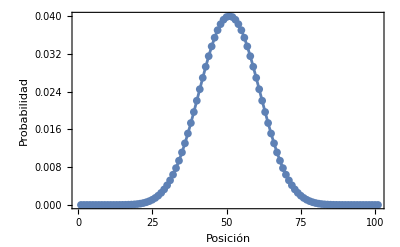

```mathematica
ListLinePlot[probsO0[[-1]],
PlotRange->All,
Mesh->All,
Frame->True,
Axes->False,
FrameLabel->{"Posición","Probabilidad"}
]
```

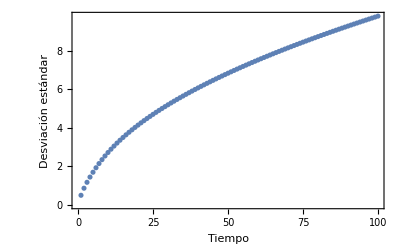

```mathematica
ListPlot[sdsO0,
PlotRange->All,
Frame->True,
Axes->False,
FrameLabel->{"Tiempo","Desviación estándar"}
]
```

```mathematica
DTQWSdAdjustments[sdsO0]
```

FittedModel[0.965672 √x]

### More probs

#### p = 0.1

```mathematica
envO1=DTQWEnv[<|
"Type"->"ForwardGrowing","Decoherent"->True,"Unitary"->UnitaryOperator,
"Probabilities"->{0.9,0.1},
"Kraus"->{IdentityMatrix[2*#,SparseArray]&,PositionprojOperator}
|>];
```

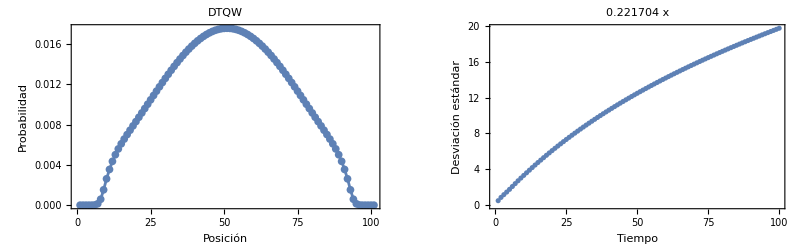

```mathematica
coinO1={1,ⅈ}/Sqrt[2.];
DTQWSummary[coinO1,envO1]
```

```mathematica
Export["/home/amadoc/Desktop/progra/Mathematica/quantum_walks/AmadoTemp/EPS/results/img/PosProjectionQW_0-1.pdf",%]
```

/home/amadoc/Desktop/progra/Mathematica/quantum_walks/AmadoTemp/EPS/results/img/PosProjectionQW_0-1.pdf

#### p = 0.01

```mathematica
envO2=DTQWEnv[<|
"Type"->"ForwardGrowing","Decoherent"->True,"Unitary"->UnitaryOperator,
"Probabilities"->{0.99,0.01},
"Kraus"->{IdentityMatrix[2*#,SparseArray]&,PositionprojOperator}
|>];
```

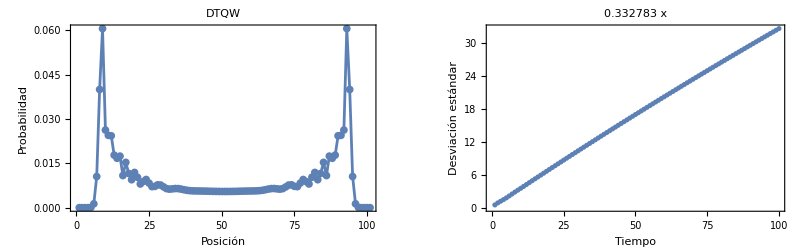

```mathematica
coinO2={1,ⅈ}/Sqrt[2.];
DTQWSummary[coinO2,envO2]
```

```mathematica
Export["/home/amadoc/Desktop/progra/Mathematica/quantum_walks/AmadoTemp/EPS/results/img/PosProjectionQW_0-01.pdf",%]
```

/home/amadoc/Desktop/progra/Mathematica/quantum_walks/AmadoTemp/EPS/results/img/PosProjectionQW_0-01.pdf

#### p = 0.02

```mathematica
envO3=DTQWEnv[<|
"Type"->"ForwardGrowing","Decoherent"->True,"Unitary"->UnitaryOperator,
"Probabilities"->{0.98,0.02},
"Kraus"->{IdentityMatrix[2*#,SparseArray]&,PositionprojOperator}
|>];
```

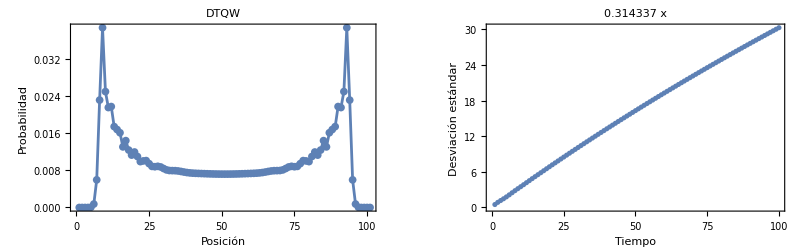

```mathematica
coinO3={1,ⅈ}/Sqrt[2.];
DTQWSummary[coinO3,envO3]
```

```mathematica
Export["/home/amadoc/Desktop/progra/Mathematica/quantum_walks/AmadoTemp/EPS/results/img/PosProjectionQW_0-02.pdf",%]
```

/home/amadoc/Desktop/progra/Mathematica/quantum_walks/AmadoTemp/EPS/results/img/PosProjectionQW_0-02.pdf

#### p = 0.05

```mathematica
envO4=DTQWEnv[<|
"Type"->"ForwardGrowing","Decoherent"->True,"Unitary"->UnitaryOperator,
"Probabilities"->{0.95,0.05},
"Kraus"->{IdentityMatrix[2*#,SparseArray]&,PositionprojOperator}
|>];
```

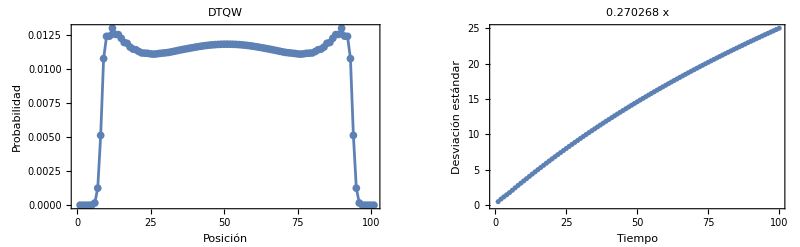

```mathematica
coinO4={1,ⅈ}/Sqrt[2.];
DTQWSummary[coinO4,envO4]
```

```mathematica
Export["/home/amadoc/Desktop/progra/Mathematica/quantum_walks/AmadoTemp/EPS/results/img/PosProjectionQW_0-05.pdf",%]
```

/home/amadoc/Desktop/progra/Mathematica/quantum_walks/AmadoTemp/EPS/results/img/PosProjectionQW_0-05.pdf

#### p = 0.07

```mathematica
envO5=DTQWEnv[<|
"Type"->"ForwardGrowing","Decoherent"->True,"Unitary"->UnitaryOperator,
"Probabilities"->{0.93,0.07},
"Kraus"->{IdentityMatrix[2*#,SparseArray]&,PositionprojOperator}
|>];
```

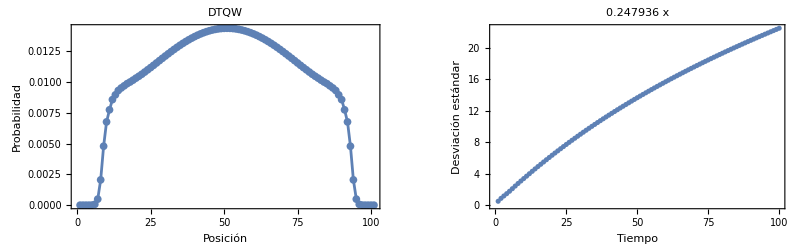

```mathematica
coinO5={1,ⅈ}/Sqrt[2.];
DTQWSummary[coinO5,envO5]
```

```mathematica
Export["/home/amadoc/Desktop/progra/Mathematica/quantum_walks/AmadoTemp/EPS/results/img/PosProjectionQW_0-07.pdf",%]
```

/home/amadoc/Desktop/progra/Mathematica/quantum_walks/AmadoTemp/EPS/results/img/PosProjectionQW_0-07.pdf

#### p = 1

```mathematica
envO6=DTQWEnv[<|
"Type"->"ForwardGrowing","Decoherent"->True,"Unitary"->UnitaryOperator,
"Probabilities"->{0,1},
"Kraus"->{IdentityMatrix[2*#,SparseArray]&,PositionprojOperator}
|>];
```

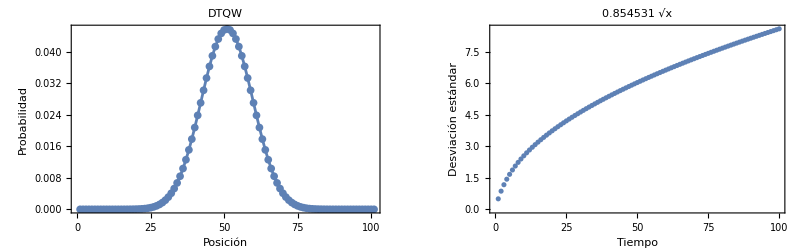

```mathematica
coinO6={1,ⅈ}/Sqrt[2.];
DTQWSummary[coinO6,envO6]
```

```mathematica
Export["/home/amadoc/Desktop/progra/Mathematica/quantum_walks/AmadoTemp/EPS/results/img/PosProjectionQW_1.pdf",%]
```

/home/amadoc/Desktop/progra/Mathematica/quantum_walks/AmadoTemp/EPS/results/img/PosProjectionQW_1.pdf

### Measuring DTQW Quanticity

```mathematica
coinO7={1,ⅈ}/Sqrt[2.];
desv=DTQWQuanticity[coinO7,Range[0,1,0.01]];
```

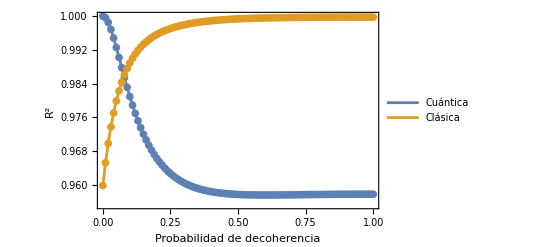

```mathematica
ListLinePlot[{#[[All,{1,2}]],#[[All,{1,3}]]}&[desv],
Frame->True,
Axes->False,
Mesh->All,
PlotLegends->{"Cuántica","Clásica"},
FrameLabel->{"Probabilidad de decoherencia","R^2"}
]
```

```mathematica
Export["/home/amadoc/Desktop/progra/Mathematica/quantum_walks/AmadoTemp/EPS/results/img/PosProjectionQW_quanticity.pdf",%]
```

/home/amadoc/Desktop/progra/Mathematica/quantum_walks/AmadoTemp/EPS/results/img/PosProjectionQW_quanticity.pdf

### Matrix plot collage

#### Code

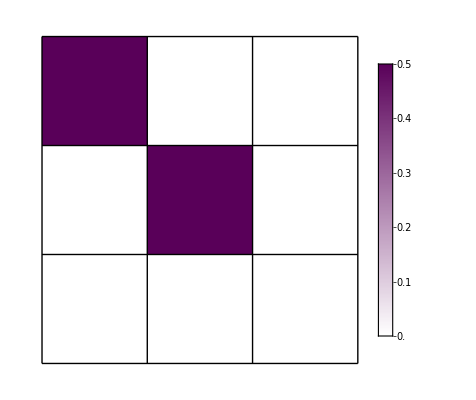
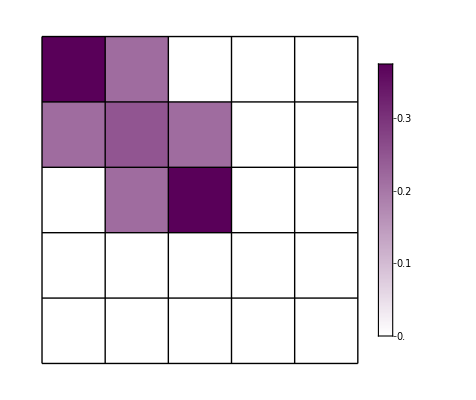
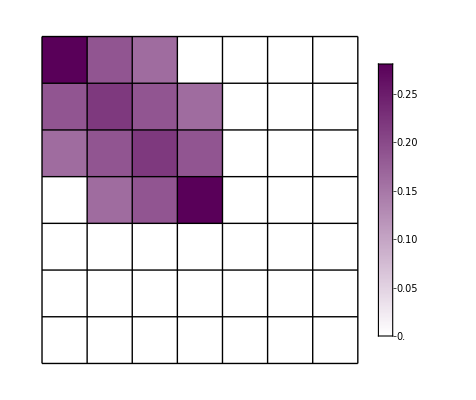
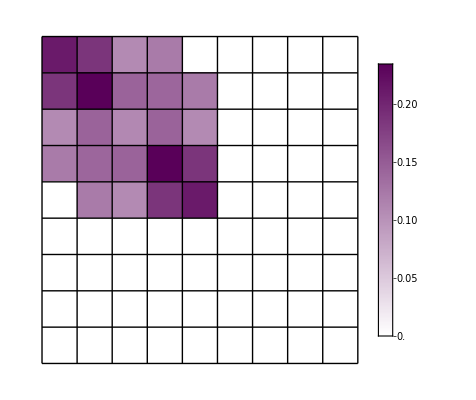
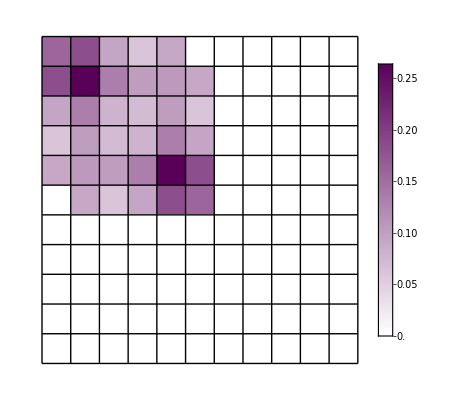
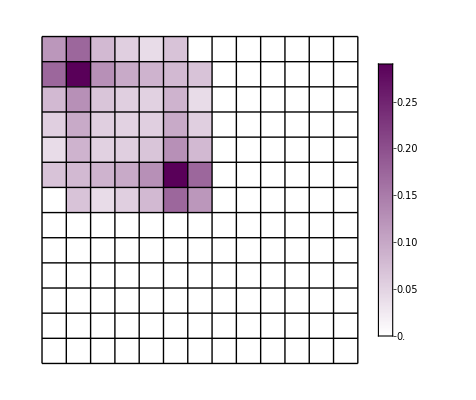
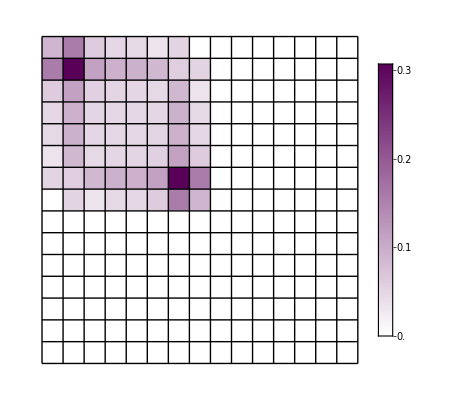
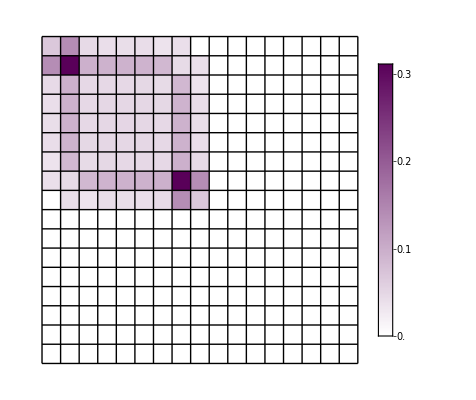

```mathematica
envO8=DTQWEnv[<|
"Type"->"TwoAhead","Decoherent"->True,"Unitary"->UnitaryOperator,
"Probabilities"->{1,0},
"Kraus"->{IdentityMatrix[2*#,SparseArray]&,FuzzyOperator}
|>];
coinO8={1,ⅈ}/Sqrt[2.];
a=DTQWMatrixPlot[coinO8,10,envO8,2]
```

```mathematica
envO8=DTQWEnv[<|
"Type"->"TwoAhead","Decoherent"->True,"Unitary"->UnitaryOperator,
"Probabilities"->{0.9,0.1},
"Kraus"->{IdentityMatrix[2*#,SparseArray]&,FuzzyOperator}
|>];
coinO8={1,ⅈ}/Sqrt[2.];
b=DTQWMatrixPlot[coinO8,10,envO8,2];
```

```mathematica
envO8=DTQWEnv[<|
"Type"->"TwoAhead","Decoherent"->True,"Unitary"->UnitaryOperator,
"Probabilities"->{0.8,0.2},
"Kraus"->{IdentityMatrix[2*#,SparseArray]&,FuzzyOperator}
|>];
coinO8={1,ⅈ}/Sqrt[2.];
c=DTQWMatrixPlot[coinO8,10,envO8,2];
```

```mathematica
envO8=DTQWEnv[<|
"Type"->"TwoAhead","Decoherent"->True,"Unitary"->UnitaryOperator,
"Probabilities"->{0.7,0.3},
"Kraus"->{IdentityMatrix[2*#,SparseArray]&,FuzzyOperator}
|>];
coinO8={1,ⅈ}/Sqrt[2.];
d=DTQWMatrixPlot[coinO8,10,envO8,2];
```

```mathematica
envO8=DTQWEnv[<|
"Type"->"TwoAhead","Decoherent"->True,"Unitary"->UnitaryOperator,
"Probabilities"->{0.6,0.4},
"Kraus"->{IdentityMatrix[2*#,SparseArray]&,FuzzyOperator}
|>];
coinO8={1,ⅈ}/Sqrt[2.];
e=DTQWMatrixPlot[coinO8,10,envO8,2];
```

```mathematica
envO8=DTQWEnv[<|
"Type"->"TwoAhead","Decoherent"->True,"Unitary"->UnitaryOperator,
"Probabilities"->{0.5,0.5},
"Kraus"->{IdentityMatrix[2*#,SparseArray]&,FuzzyOperator}
|>];
coinO8={1,ⅈ}/Sqrt[2.];
f=DTQWMatrixPlot[coinO8,10,envO8,2];
```

#### Collage

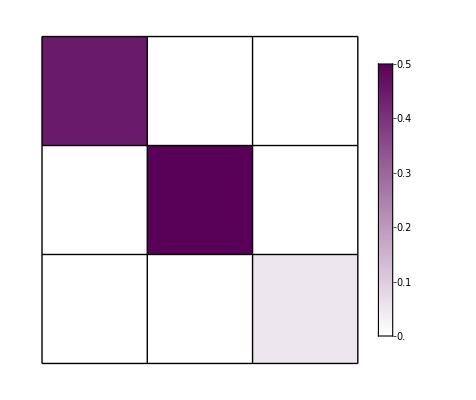
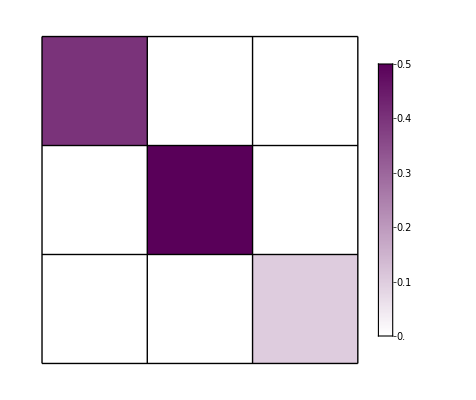
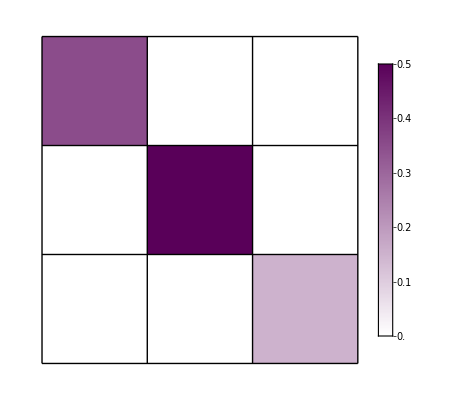
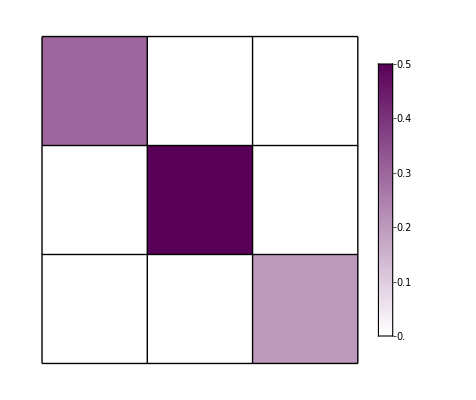
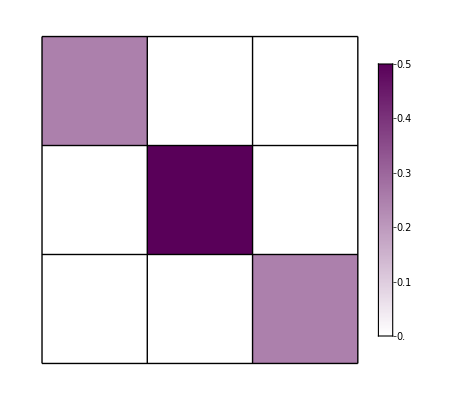
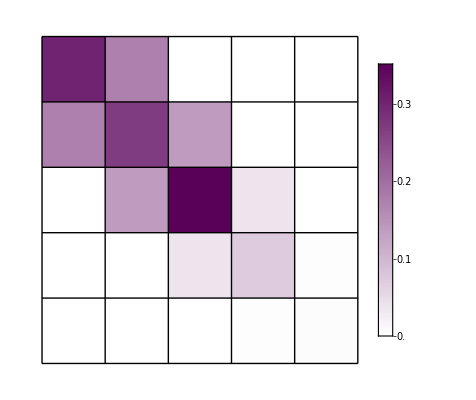
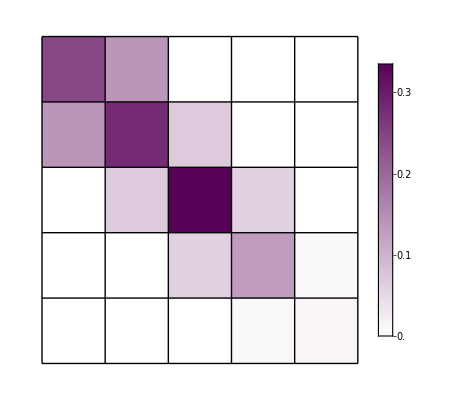
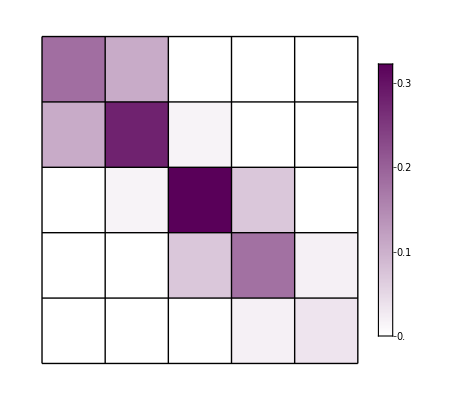
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Transpose[{a,b,c,d,e,f}[[{1,2,3,4,5,6}]]]//TableForm
```

```mathematica
Export["/home/amadoc/Desktop/progra/Mathematica/quantum_walks/AmadoTemp/EPS/results/img/FuzzyQW_1sDM_0.pdf",a[[1]]]
Export["/home/amadoc/Desktop/progra/Mathematica/quantum_walks/AmadoTemp/EPS/results/img/FuzzyQW_10sDM_0.pdf",a[[-1]]]
Export["/home/amadoc/Desktop/progra/Mathematica/quantum_walks/AmadoTemp/EPS/results/img/FuzzyQW_1sDM_0-5.pdf",f[[1]]]
Export["/home/amadoc/Desktop/progra/Mathematica/quantum_walks/AmadoTemp/EPS/results/img/FuzzyQW_10sDM_0-5.pdf",f[[-1]]]
```

/home/amadoc/Desktop/progra/Mathematica/quantum_walks/AmadoTemp/EPS/results/img/FuzzyQW_1sDM_0.pdf

/home/amadoc/Desktop/progra/Mathematica/quantum_walks/AmadoTemp/EPS/results/img/FuzzyQW_10sDM_0.pdf

/home/amadoc/Desktop/progra/Mathematica/quantum_walks/AmadoTemp/EPS/results/img/FuzzyQW_1sDM_0-5.pdf

/home/amadoc/Desktop/progra/Mathematica/quantum_walks/AmadoTemp/EPS/results/img/FuzzyQW_10sDM_0-5.pdf

#### Just one image

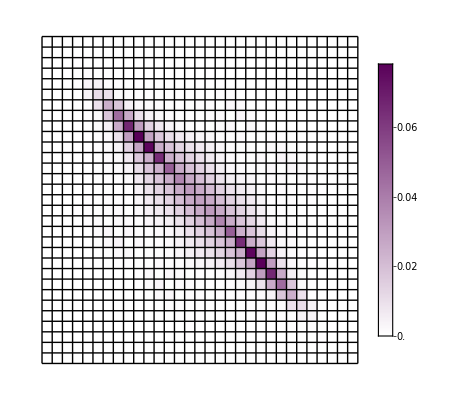

```mathematica
envO9=DTQWEnv[<|
"Type"->"TwoAhead","Decoherent"->True,"Unitary"->UnitaryOperator,
"Probabilities"->{0.5,0.5},
"Kraus"->{IdentityMatrix[2*#,SparseArray]&,FuzzyOperator}
|>];
coinO9={1,ⅈ}/Sqrt[2.];
ArrayPlot[#,
PlotLegends->Automatic,
ColorFunction->(Blend[{White,Blend[{Purple,Black},0.3]},#]&),
Mesh->True,
MeshStyle->Black
]&@Abs[(MatrixPartialTrace[#,2,{Round[Length[#]/2],2}]&@DTQW[coinO9,15,envO9])]
```

### Different shifts

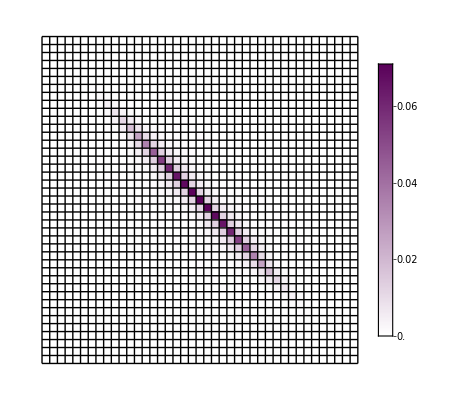

```mathematica
p10=0.5;
env10=DTQWEnv[<|
"Type"->"FourAhead","Decoherent"->True,"Unitary"->UnitaryOperator,
"Probabilities"->{1/4,1/4,1/4,1/4},
"Kraus"->{IdentityMatrix[2*#,SparseArray]&,PermutationOperators[1],PermutationOperators[2],PermutationOperators[3]}
|>];
coin10={1,ⅈ}/Sqrt[2.];
steps10=MatrixPartialTrace[#,2,{Round[Length[#]/2],2}]&/@DTQWTrace[coin10,10,env10];
(ArrayPlot[#,
PlotLegends->Automatic,
ColorFunction->(Blend[{White,Blend[{Purple,Black},0.3]},#]&),
Mesh->True,
MeshStyle->Black
]&/@Abs[steps10])[[-1]]
```

```mathematica
Export["/home/amadoc/Desktop/progra/Mathematica/quantum_walks/AmadoTemp/EPS/results/img/FuzzyQW_4permutation_10sDM.pdf",%]
```

/home/amadoc/Desktop/progra/Mathematica/quantum_walks/AmadoTemp/EPS/results/img/FuzzyQW_4permutation_10sDM.pdf

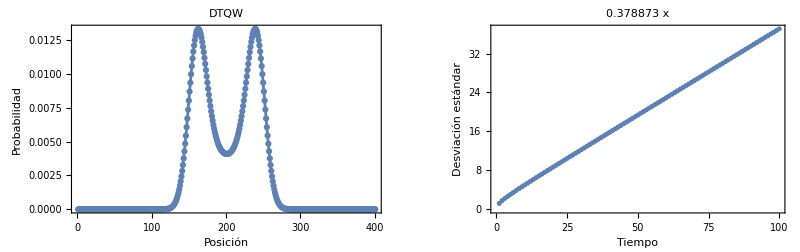

```mathematica
DTQWSummary[coin10,env10]
```

```mathematica
Export["/home/amadoc/Desktop/progra/Mathematica/quantum_walks/AmadoTemp/EPS/results/img/FuzzyQW_4permutation.pdf",%]
```

/home/amadoc/Desktop/progra/Mathematica/quantum_walks/AmadoTemp/EPS/results/img/FuzzyQW_4permutation.pdf